```mathematica
(*Pauli 矩阵*)
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];

(*在第 pos 位作用的算符*)
KronMultiple[op_,pos_,Num_]:=KroneckerProduct@@Table[If[i==pos,op,IdentityMatrix[2]],{i,1,Num}];


QuantumXYHamiltonian[Num_,γ_,Jsum_,h_,boundarycond_,phi_:0]:=Jsum/4 Module[{dim=2^Num,H,neighbors,twistTerm,interactionTerm,fieldTerm},(*生成所有相邻格点对*)neighbors=Switch[boundarycond,"PBC",Table[{i,Mod[i,Num]+1},{i,1,Num}],"OBC"|"TwistBC",Table[{i,i+1},{i,1,Num-1}]];
(*相互作用项*)interactionTerm=Total[Table[(1+γ)/2*(KronMultiple[σx,neighbors[[kk,1]],Num].KronMultiple[σx,neighbors[[kk,2]],Num])+(1-γ)/2*(KronMultiple[σy,neighbors[[kk,1]],Num].KronMultiple[σy,neighbors[[kk,2]],Num]),{kk,1,Length[neighbors]}]];
(*扭曲边界最后一项*)twistTerm=If[boundarycond=="TwistBC",Module[{ii=Num,jj=1},Exp[ⅈ phi]*(1+γ)/2*(KronMultiple[σx,ii,Num].KronMultiple[σx,jj,Num])+Exp[ⅈ phi]*(1-γ)/2*(KronMultiple[σy,ii,Num].KronMultiple[σy,jj,Num])],0];
(*外磁场项*)fieldTerm=Total[Table[h*KronMultiple[σz,ii,Num],{ii,1,Num}]];
(*总哈密顿量*)H=-interactionTerm-twistTerm+fieldTerm;
H];
```

```mathematica
L = 6;
Jsum=4;
Clear[β];

ϕ=10^-3;
Zp=Total[Exp[-β*Eigenvalues[QuantumXYHamiltonian[L,γ,Jsum,h,"TwistBC",ϕ]]]];
Fp=-Log[Zp]/β;
Zm=Total[Exp[-β*Eigenvalues[QuantumXYHamiltonian[L,γ,Jsum,h,"TwistBC",-ϕ]]]];
Fm=-Log[Zm]/β;
Z0=Total[Exp[-β*Eigenvalues[QuantumXYHamiltonian[L,γ,Jsum,h,"TwistBC",0]]]];
F0=-Log[Z0]/β;

Dq=1/(2L)(Fp-2F0+Fm)/ϕ^2
```

$Aborted

$Aborted

$Aborted

```mathematica
Dq=1/(2L)(Fp-2F0+Fm)/ϕ^2/.{β->100}//N
```

0.0650933+2.32329×10^-14 ⅈ

```mathematica
Plot3D
```

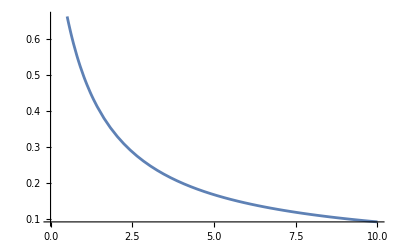

```mathematica
Plot[1/(1+x),{x,0,10}]
```